```mathematica
fn[x_]:=2/Pi*ArcSin[Sqrt[x]]
```

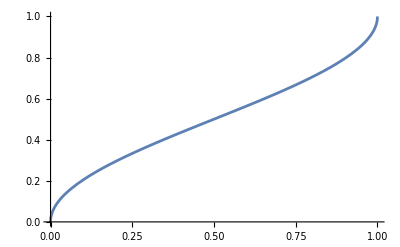

```mathematica
Plot[fn[x],{x,0,1}]
```

```mathematica
fm[x_]:=Piecewise[{{0,x<0},{fn[x],0<=x<=1},{1,x>1}} ]
```

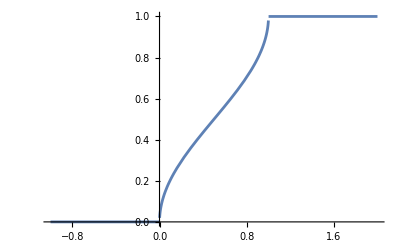

```mathematica
Plot[fm[x],{x,-1,2}]
```

```mathematica
X=ProbabilityDistribution[{"CDF",2/Pi*ArcSin[Sqrt[x]]},{x,0,1}]
```

ProbabilityDistribution[Piecewise[{{1/(√(1-x) √x π), 0<x<1}, {0, True}}],{x,0,1}]

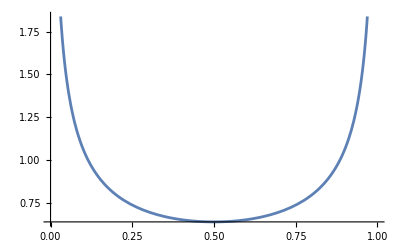

```mathematica
Plot[PDF[ProbabilityDistribution[{"CDF",2/Pi*ArcSin[Sqrt[x]]},{x,-1,2}],z],{z,0,1}]
```